# Woods - Saxon Potential

```mathematica
f[r_,r0_,a_,A_]:=1/(1+Exp[(r-r0 A^(1/3))/a])
```

```mathematica
Manipulate[
Plot[-f[r,r0,a,A],{r,0,4},PlotRange->All]
,{{r0,1},0.5,2},{{A,4},1,10},{{a,0.1},0.01,0.5}]
```

```mathematica
(* Hamiltonian for Helium *)
(1/r^2∂/(∂r)(r^2∂/(∂r))-1/r^2 L^2-V0 f[r,1,0.1,4])ψ[r,θ,ϕ]== Ε ψ[r,θ,ϕ]
```

```mathematica
(* seperating varible *)
ψ[r,θ,ϕ] ==R[r]Y[l,m,θ,ϕ]
(* we have decoupled equation *)
(1/r^2 ⅆ/ⅆr(r^2 ⅆ/ⅆr)-(l(l+1))/r^2-V0 f[r,1,0.1,4])R[r]==-(2m Ε)/ℏ^2 R[r]
L^2 Y[l,m,θ,ϕ]== l(l+1) Y[l,m,θ,ϕ]
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
(ⅆ/ⅆr(r^2 ⅆ/ⅆr)+(2m Ε)/ℏ^2 r^2-l(l+1)-V0 f[r,1,0.1,4] r^2)R[r]==0
```

```mathematica
Clear[sol]
```

```mathematica
sol[k_,V0_,l_]:=NDSolve[{r^2 R''[r]+2r R'[r]+ (k^2 r^2-l(l+1)-V0  f[r,1,0.1,4] r^2)R[r]==0,R'[0.1]==5,R[30]==0},R,{r,0.1,4}]
```

```mathematica
s=sol[1,1,0]
```

{{R→InterpolatingFunction[{{0.1,4.}},<>]}}

```mathematica
R[0.4]/.s
```

{1.}

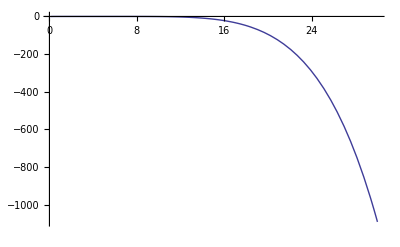

```mathematica
Plot[Evaluate[R[r]/.s],{r,0.1,30},PlotRange->All]
```